#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_SDistAll.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Nano_CSM_Biosensor.wls"
<<"~/Documents/Wolfram/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

/home/juanathan/Documents/Collaborations/En progreso/2022-06-INAOE-CSM/4-Sustrato-Comsol

```mathematica
fs = 10;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors = Flatten@Prepend[colors,{Red,Darker[Green]}]
```

{RGBColor[1, 0, 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

```mathematica
em[name_String, size_ : 7] := 
  ResourceFunction["PolygonMarker"][name, 
   Offset[size], {Dynamic@
     EdgeForm[{CurrentValue["Color"], JoinForm["Round"], 
       AbsoluteThickness[1], Opacity[1]}], FaceForm[White]}, 
   ImagePadding -> 6];
```

### Incrustamiento

{5.78,7.3}

{3.3,4.5}

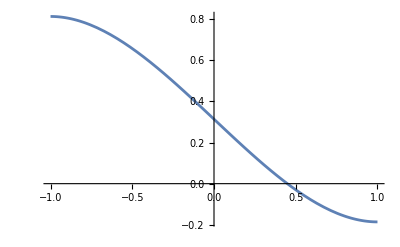
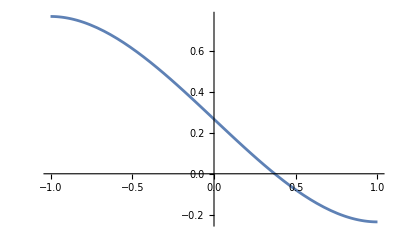

{{h→0.448624},{h→0.371421}}

{2.59304,2.71137}

```mathematica
scaleFactor[h_]:=0.5 - 0.75*h + 0.25*h*h*h ; (*h -> Incrustation factor: h/a. h Distance between center and interface, a AuNP radius*)
radiusM = {5.78, 7.30}
radiusF = {3.3, 4.5}

Plot[scaleFactor[h]-# ,{h,-1,1}]& /@ ((radiusF/radiusM)^3)
FindRoot[scaleFactor[h]-#^3 == 0, {h,.1} ] & /@ (radiusF/radiusM)
(h /. %)*radiusM
```

{5.78,7.3}

{3.5,4.5}

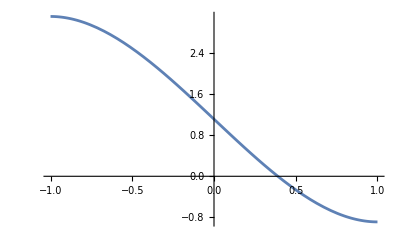
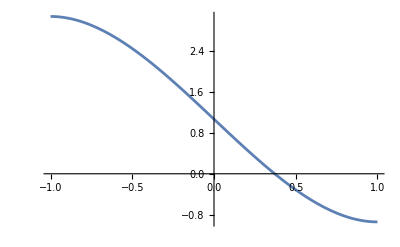

{{h→0.390464},{h→0.371421}}

{2.25688,2.71137}

```mathematica
scaleFactor[h_]:=(1.-2.*h+h*h)*(2.+h) ; (*h -> Incrustation factor: h/a. h Distance between center and interface, a AuNP radius*)
radiusM = {5.78, 7.30}
radiusF = {3.5, 4.5}

Plot[scaleFactor[h]-4*# ,{h,-1,1}]& /@ ((radiusF/radiusM)^3)
FindRoot[scaleFactor[h]-4*#^3 == 0, {h,.1} ] & /@ (radiusF/radiusM)
(h /. %)*radiusM
```

### Mie vs Substrate

```mathematica
radius = {5.78, 7.3};
nNP = JohnsonChristyAuRefSize[#1, #2] &;

scaQ[lda_,radius_]:= Map[MieScatteringQ[{1., nNP[#, radius]}, #, radius]&, lda]
extQ[lda_,radius_]:= Map[MieExtinctionQ[{1., nNP[#, radius]}, #, radius]&, lda]
```

```mathematica
FileNames["E*.csv","IncidenciaNormal"]
data = Import[#,"Data"] & /@ FileNames["E*.csv","IncidenciaNormal"]; (*Import both files*)
data = Transpose[Drop[#,5,{1}]] & /@ data; (*[[radius, lda, abs, sca]]*)
 
wlen = data[[1,1]] (*create lda*);
wlenMie = Range[#1,#2,.25]&@@wlen[[{1,-1}]];

data = data[[;;,{2,3}]]; (* [[radius, abs, sca]]*)
data = Apply[Plus,data,{1}] (*[[radius, abs + sca = ext]]*);
dataMie = extQ[wlenMie,#] & /@ radius;
```

{IncidenciaNormal/Efficiencies-5nm.csv,IncidenciaNormal/Efficiencies-7nm.csv}

```mathematica
FileNames["I*.csv","IncidenciaNormal"]
data2 = Import[#,"Data"] & /@ FileNames["I*.csv","IncidenciaNormal"]; (*Import both files*)
data2 = Transpose[Drop[#,5,{1}]] & /@ data2; (*[[radius, lda, abs, sca]]*)
 
wlen2 = data2[[1,1]] (*create lda*);

data2 = data2[[;;,{2,3}]]; (* [[radius, abs, sca]]*)
data2 = Apply[Plus,data2,{1}] (*[[radius, abs + sca = ext]]*);
```

{IncidenciaNormal/Inc-Efficiencies-5nm.csv,IncidenciaNormal/Inc-Efficiencies-7nm.csv}

```mathematica
plots = ConstantArray[0,6];

graphsOptsMie = {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#]&/@colors)};
graphsOptsFEM = {Mesh-> All,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors),
                PlotMarkers-> em[#,2.5]&/@{"Disk"}};
graphsOptsFEM2 = {Mesh-> None,BaseStyle-> texStyle,Frame-> True,
                FrameStyle-> Black,ImageSize-> 685*2/5, PlotStyle-> (Directive[#,Thin]&/@colors),PlotMarkers-> em[#,2.5]&/@{"Circle"}
                 };

extMie = Transpose[{wlenMie,#}] & /@ dataMie;
maxMie = MaximalBy[#,Last] & /@ extMie
extFEM = Transpose[{wlen,#}] & /@ data;
maxFEM = MaximalBy[#,Last] & /@ extFEM
extFEM2 = Transpose[{wlen2,#}] & /@ data2;
maxFEM2 = MaximalBy[#,Last] & /@ extFEM2

plots[[1]] = ListLinePlot[#,Evaluate[graphsOptsMie]]& @ extMie;
plots[[2]] = ListLinePlot[#,Evaluate[graphsOptsFEM]]& @ extFEM;
plots[[3]] = ListLinePlot[#,Evaluate[graphsOptsFEM2]]& @ extFEM2[[;;,4;;-11]];
plots[[4]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxMie,1], PlotStyle-> Directive[Magenta,PointSize[.025]] ];
plots[[5]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxFEM,1],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
plots[[6]] = ListPlot[Callout[#,NumberForm[First[#],{5,2}],Right,LabelStyle->texStyle]& /@ Flatten[maxFEM2,1],PlotStyle-> Directive[Magenta,PointSize[.025]]  ];
```

{{{509.75,0.20717}},{{509.5,0.272552}}}

{{{512.5,0.152594}},{{512.5,0.201922}}}

{{{523.5,0.431966}},{{523.75,0.578933}}}

### Figures

```mathematica
fplot = Show[plots[[{1,2,4,5}]],AspectRatio->1,ImageSize-> 250*.715,PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
Export["Mie-vs-Comsol-Supported.svg",fplot]
```

-Graphics-

Mie-vs-Comsol-Supported.svg

```mathematica
fplot = Show[plots[[{1,3,4,6}]],AspectRatio->1/GoldenRatio,ImageSize-> 250*1.05, PlotRange->All, FrameLabel -> (Style[#,texStyle]&/@{"Wavelength [nm]","Extinction Efficiencies"}) ]
Export["Mie-vs-Comsol-Embedded.svg",fplot]
```

-Graphics-

Mie-vs-Comsol-Embedded.svg